```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["examples.dat"];
```

```mathematica
Dimensions[data]
```

{50001,12}

```mathematica
x=Flatten[Take[data,{1,50000},{3}]];
y=Flatten[Take[data,{1,50000},{4}]];
```

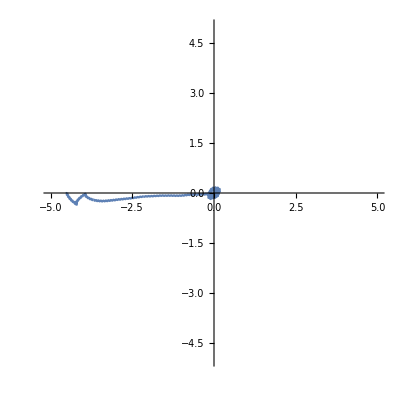

```mathematica
ListLinePlot[Transpose[{x,y}],AspectRatio->True,PlotRange->{{-5,5},{-5,5}}]
```